# Fourier Sine Series

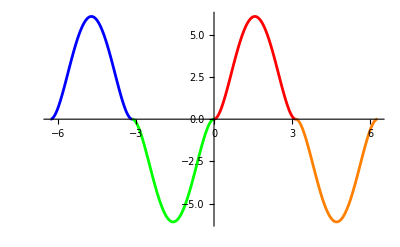

```mathematica
Clear[f,x]
f[x_]:=If[0<x<π,x^2(π-x)^2,10]
Show[
Plot[f[x],{x,0,π},PlotStyle->Red],
Plot[-f[-x],{x,-π,0},PlotStyle->Green],
Plot[-f[x-π],{x,Pi,2 π},PlotStyle->Orange],
Plot[f[x+2π],{x,-2Pi,-π},PlotStyle->Blue],
PlotRange->All
]
```

```mathematica
Integrate[f[x] Sin[n x],{x,0,π}]
```

(-2 n π-4 n π Cos[n π]+(6-n^2 π^2) Sin[n π])/n^4

```mathematica
Simplify[ Integrate[f[x] Sin[n x],{x,0,π}],n∈Integers]
```

-(2 (1+2 (-1)^n) π)/n^3

```mathematica
Simplify[ Integrate[f[x] Sin[n x],{x,0,π}],Element[n,Integers]]
```

-(2 (1+2 (-1)^n) π)/n^3